# Convergence Rates

We need to make sure people have a clear understanding of convergence rates and their practical importance.

## Newtons Method

If I want to solve 
	f(x)=0
then I can think about starting from a guess x_k and improving it to get a hopefully better x_(k+1) by solving where the linearization
	f(x_k)+f'(x_k)(x-x_k)
equals zero.  This gives the Newton iteration
	x_(k+1)=x_k-f(x_k)/f'(x_k).
This works the same for the system of m equations in m unknowns that you get if you consider x∈ℝ^m and f:ℝ^m→ℝ^m and ∇f(x_k)∈ℝ^(m×m).
	x_(k+1)=x_k-LinearSolve[∇f(x_k),f(x_k)]
We are going to see how fast these iterations converge!

### 1D Newton

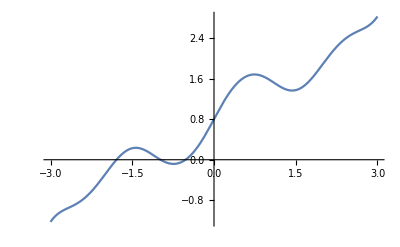

```mathematica
f[x_]:= Sin[x Cos[x+ArcTan[x]]]+ 0.8+ x
Plot[f[x],{x,-3,3}]
```

```mathematica
x0=0.8;
{xVal,fRes}={x,f[x]}/.FindRoot[f[x]==0,{x, x0}];
xk=x0;
TableForm[
Data=Table[
xk=xk-f[xk]/f'[xk];
{xk,xk-xVal,Abs[f[xk]]},{20}],
TableHeadings->{Automatic,{"x_k","||x_k-xVal||","|f[x_k]|"}}]
```

| x_k | ||x_k-xVal|| | |f[x_k]|
1 | 9.98856 | 10.5119 | 9.81775
2 | 17.7128 | 18.2361 | 17.8263
3 | 14.2096 | 14.733 | 14.0123
4 | 1.11512 | 1.63843 | 1.50932
5 | 3.24519 | 3.7685 | 3.45619
6 | 2.29541 | 2.81872 | 2.27723
7 | 0.176255 | 0.699563 | 1.14103
8 | -0.454623 | 0.0686848 | 0.0601891
9 | -0.515121 | 0.00818644 | 0.00631308
10 | -0.523159 | 0.000149107 | 0.00011289
11 | -0.523308 | 5.13572×10^-8 | 3.88696×10^-8
12 | -0.523308 | 6.10623×10^-15 | 4.55191×10^-15
13 | -0.523308 | 1.11022×10^-16 | 0.
14 | -0.523308 | 1.11022×10^-16 | 0.
15 | -0.523308 | 1.11022×10^-16 | 0.
16 | -0.523308 | 1.11022×10^-16 | 0.
17 | -0.523308 | 1.11022×10^-16 | 0.
18 | -0.523308 | 1.11022×10^-16 | 0.
19 | -0.523308 | 1.11022×10^-16 | 0.
20 | -0.523308 | 1.11022×10^-16 | 0.

### 2D Newton

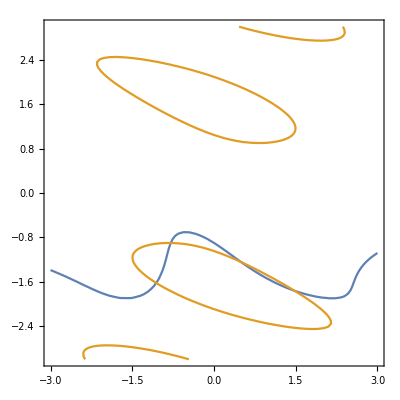

```mathematica
Clear[f,x,y]
f[{x_,y_}]:= {Sin[x Cos[y+ArcTan[x]]]+ 0.9+ y, x^2 + 2 y Sin[x+3y]}
df[{x_,y_}]= D[f[{x,y}],{{x,y}}];
ContourPlot[{f[{x,y}]⟦1⟧==0,f[{x,y}]⟦2⟧==0},{x,-3,3},{y,-3,3},ContourShading->False]
```

```mathematica
x0={-1.622,0.84};
{xVal,fRes}={{x,y},f[{x,y}]}/.FindRoot[f[{x,y}]==0,{{x,y},x0}ᵀ ];
xk=x0;
TableForm[
Data=Table[
xk=xk-LinearSolve[df[xk],f[xk]];
{Norm[xk-xVal],Norm[f[xk]]},{20}],
TableHeadings->{Automatic,{"||x_k-xVal||","||f[x_k]||"}}]
```

| ||x_k-xVal|| | ||f[x_k]||
1 | 2.32801 | 1.74926
2 | 0.645938 | 0.378721
3 | 5.92288 | 43.2541
4 | 2.98642 | 7.06194
5 | 1.69019 | 1.46165
6 | 1.25408 | 0.173456
7 | 1.12351 | 0.0130927
8 | 1.10877 | 0.00016065
9 | 1.10857 | 2.85656×10^-8
10 | 1.10857 | 4.96507×10^-16
11 | 1.10857 | 4.96507×10^-16
12 | 1.10857 | 2.22045×10^-16
13 | 1.10857 | 1.79018×10^-15
14 | 1.10857 | 1.77636×10^-15
15 | 1.10857 | 2.22045×10^-16
16 | 1.10857 | 1.79018×10^-15
17 | 1.10857 | 1.77636×10^-15
18 | 1.10857 | 2.22045×10^-16
19 | 1.10857 | 1.79018×10^-15
20 | 1.10857 | 1.77636×10^-15

## Bisection Method

If I want to solve 
	f(x)=0
then I can bracket the root in an interval (a_k,b_k)  f(a_k)f(b_k)<0 and we are going to preserve this property as follows.  Evaluate f((a_k+b_k)/2) and relace the appropriate endpoint by (a_k+b_k)/2.

```mathematica
BiStep[f][{{a_,b_},{fa_,fb_}}]:= Module[{z=0.5*(a+b),fz},
fz=f[z];  
If[ f[z]*fa>0, {{z,b},{fz,fb}}, {{a,z},{fa,fz}}]
]
```

## Secant Method

If I want to solve 
	f(x)=0
then I can